```mathematica
SetDirectory["/Users/tomasdecaminobeck/Documents/Wolfram Mathematica/CATIE data/"];
```

```mathematica
data=Drop[Drop[Import["CATIELidarB1.txt","CSV"],-1],2];
```

```mathematica
Length[data]
```

40905

```mathematica
data[[2]]
```

{244.05,461.}

```mathematica
dataRad=({#[[1]] Degree,#[[2]]})&/@data;
```

```mathematica
dataRad[[1]]
```

{4.25948,462.}

```mathematica
XYdata=({#[[2]]Cos[#[[1]]],#[[2]]Sin[#[[1]]]})&/@dataRad//N
```

{{-202.165,-415.419},{-201.727,-414.52},{-201.727,-414.52},{-202.165,-415.419},40898,{-147.863,213.861},{-149.57,216.328},{-154.119,222.909}}
 |  |  |  |

```mathematica
cl=FindClusters[XYdata,Method->"NeighborhoodContraction"];
```

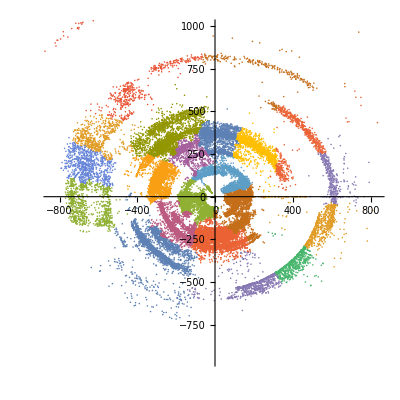

```mathematica
ListPlot[cl, AspectRatio->1]
```

```mathematica
g1=SmoothHistogram3D[cl,PlotRange->{{-1000,1000},{-1000,1000},All},Mesh->5,MeshShading->None]
```

-Graphics3D-

```mathematica
lineas={Graphics3D[{Thickness[0.01],Red, Line[{{0,0,0.00001},{1000,0,0.00001}}]}],Graphics3D[{Thick, Line[{{-1000,0,0.00001},{0,0,0.00001}}]}],Graphics3D[{Thick, Line[{{0,1000,0.00001},{0,-1000,0.00001}}]}],Graphics3D[{Thickness[0.005],Blue, Line[{{0,0,0.0000},{0,0,0.00004}}]}]};
```

```mathematica
toXY[{angle_,dist_}]:={dist Cos[angle],dist Sin[angle]};
```

```mathematica
{"angulo"," distancia"," diametro","arbol"};
dataArboles=Drop[Import["datosarbolesB.txt","CSV"],1]
```

{{265,550,75.,212},{284,130,14.1,317},{59,419,27.,325},{77,630,15.7,323},{91,489,12.5,321},{151,273,54.7,316},{162,453,13.1,315},{160,1130,20.1,411},{177,805,13.5,314},{188,590,18.5,313},{200,630,37.5,312},{226,634,37.8,311},{239,321,13.5,318}}

```mathematica
toXY[dataArboles⟦1,{1,2}⟧]//N
```

{246.426,491.706}

```mathematica
Tree[{angle_,dist_,diameter_},height_]:=Graphics3D[Cylinder[{{dist Cos[angle Degree],dist Sin[angle Degree],0},{dist Cos[angle Degree],dist Sin[angle Degree],height}},diameter]];
```

```mathematica
rodal=Table[Tree[dataArboles⟦i,{1,2,3}⟧,0.0001],{i,Length[dataArboles]}];
```

```mathematica
g2=Show[rodal]
```

-Graphics3D-

```mathematica
Manipulate[Show[Table[Tree[dataArboles⟦i,{1,2,3}⟧,300],{i,a}],lineas],{a,1,Length[dataArboles]}]
```

```mathematica
Show[g1,g2,l1a,l1b,l2,l3]
```

-Graphics3D-

## Noisy Test

```mathematica
TreeRandom[{angle_,dist_}]:={(angle+RandomVariate[NormalDistribution[0,11]])Degree,dist+RandomVariate[NormalDistribution[0,60]]}
```

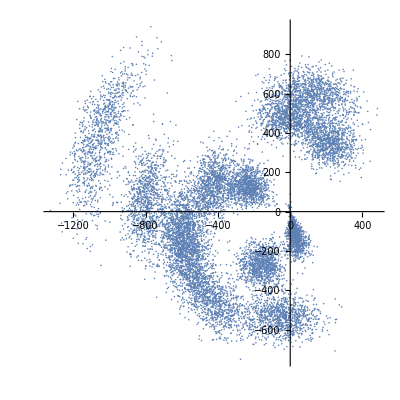

```mathematica
noisyData=Flatten[Table[toXY[TreeRandom[dataArboles⟦i,{1,2}⟧]],{1000},{i,Length[dataArboles]}],1];
ListPlot[noisyData, AspectRatio->1]
```

```mathematica
cl2=FindClusters[noisyData,Method->"NeighborhoodContraction"];
PlotRange->{{-1000,1000},{-1000,1000},All}
```

```mathematica
g3=SmoothHistogram3D[cl2,PlotRange->All,Mesh->50,MeshShading->None]
```

-Graphics3D-

```mathematica
Show[g3,g2,l1a,l1b,l2,l3]
```

-Graphics3D-

## Lidar DJI

```mathematica
dataD=Drop[Import["/Users/tomasdecaminobeck/Documents/Wolfram Mathematica/CATIE data/Datos LIdar Drone gira2/CATIE_10.TXT","CSV"],{2,15}];
```

```mathematica
Last[dataD]
```

{9.87376,-83.6648,676.5,666.73,10,12.}

```mathematica
Export["/Users/tomasdecaminobeck/Downloads/geoLidar.csv",dataD[[All,{1,2}]]]
```

/Users/tomasdecaminobeck/Downloads/geoLidar.csv

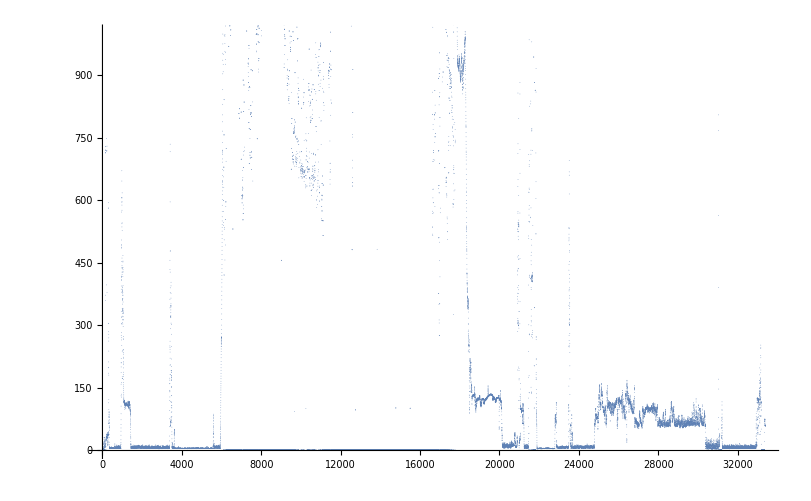

```mathematica
ListPlot[MovingAverage[dataD⟦All,3⟧,3],PlotRange->{All,1000},PlotStyle->PointSize[0.0003]]
```

## Prueba de Diámetros y muestreo DAP

```mathematica
randforest=Select[Sort[Table[{r1+RandomReal[{0,2}],r1=RandomVariate[PoissonDistribution[10]]},100000]],#⟦1⟧>10&];
```

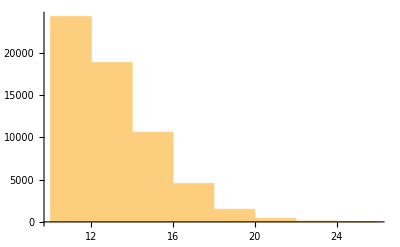

```mathematica
Histogram[randforest⟦All,1⟧,10,PlotRange->All]
```

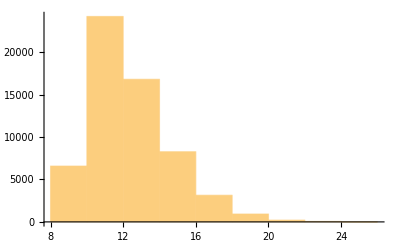

```mathematica
randsample=Table[randforest⟦i,1⟧-RandomReal[{0,0.1}]randforest⟦i,1⟧,{i,Length[randforest]}];
Histogram[randsample,10]
```